# Inheritance properties in CA increasing definitions

El objetivo de este proyecto es demostrar que existe una herencia de comportamiento que son heredados naturalmente de configuraciones iniciales. Para esto, se analizan las propiedades de las definiciones mas pequeñas de los automatas celuales y se explora la relación que tienen estos elementos en diferentes espacios y configuraciones. Para esto, el primer paso es identificar cuales sn los comportamientos existentes un automata adimensional, depsues, como estas reglas se propagan a espacios unidiemsnionales y finalmente, como el incremento de estados abre la posibildiad de universos de configuraciones intercontados con propiedades heredadas.

Como ya se menciono, el primer paso para estudiar las propiedades heredadas es necesario estudiar las propiedades de la configuración inicial. Aunque Stephen Woflram propone ECA, ciertamente esta no es la configuración minima, pues podemos tener una vecindad de 2 elementos y aun asi podemos tener 16 reglas. esta configuración con menor numero de reglas tiene menor numero de comportamientos por lo que las propiedades exhibidas aqui no suelen ser estudiadas a profundad, pues no hay secuencias pseudoaleatorias y no es Turing completo. Pero si ya definimos una vecindad de 2, ¿Es posible definir una vecindad de 1? Definir una vecindad de un unico elemento implica que solo depende del valor de una célula, pero ademas, tambien implica que puede ser vecino de si mismo, por lo que es adimensional. Pues bien, la primera parte de este experimento consiste en estudiar automatas celulares adimensionales. Mas que el comportamiento, lo que nos interesa es analizar la propagación de comportamientos.

usuaulmente los nombres de las reglas dependen de la configuración, como ECA o B3/S23 en life, pero todas las reglas pueden definirse como un numero decimal. Dado que aqui vamos a estudiar reglas que pertenecen a diferentes espacios es necesario distinguir el origen de cada una de ellas. Para iniciar usaremos la siguiente notación:

Donde la regla representa el numero decimal del vector de estados y tiene como subindices el numero de estados que requiere esa regla junto con el numero de vecinos.

## Dimensionless Cellular Automaton

## One states

Un CA que tiene un unico estado y un unico vecino solo puede tener una regla de transición posible, la regla .

```mathematica
RulePlot[CellularAutomaton[{0,1,0}],ImageSize->100,PlotLegends->Placed[Subscript[0,2,1], Below]]
```

-Graphics-

Esta regla en ese espacio es  la persistencia, no cambia, es reversible, periodica y constante. Es como un cero absoluto. Sin embargo, no podemos extraer información ni comportamientos. para esto es necesario expandir el espacio de los CAs, ya sea incrementando el numero de estados o aumentando la vecindad y la dimensionalidad, esta primera parte se enfoca en aumentar unicamente el numero de estados.

Para 2 estados, podemos generar las siguientes  reglas:

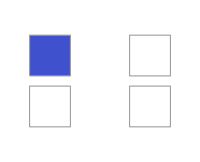
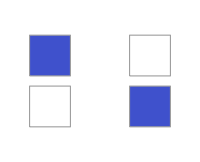
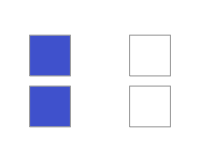
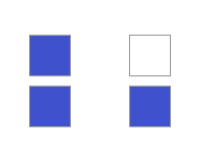
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{RulePlot[CellularAutomaton[{#,2,0}],ColorRules->colorRules,ImageSize->200,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@Range[0,3,1]}]
```

Si evolucionamos todos los sistemas con esas reglas podemos encontrar un comportamiento repetido entre la regla  y . Las cuales convierten todo a 0 y todo a 1 respectivamente, pero si hacemos una permutación en los colores (estados), obsevarvamos que obtenemos la otra regla. Para asociar todas estas reglas, utilizamos la función  InverseRules, que recibe el numero de regla, estados y numero de vecinos y devuelve todas las reglas con el mismo comportamiento. 
Adicionalmente, se puede usar la función getAlluniqueRules que solo recibe el numero de estados y de vecinos y crea todas las asociones de ese espacio de reglas. Por ejemplo, estos son los comportamientos unicos para 2 estados y un vecino:

```mathematica
getAllUniqueRules[2,1]
```

{0→{0,3},1→{1},2→{2}}

Si asumimos que el comportamiento de la regla  es el mismo que el de la regla , entonces reducimos aun mas el numero de comportamientos diferentes, sin embargo, la regla  no es reversible, por lo que no exactamente lo mismo, pero si tiene el mismo tipo de atractor. 
Las reglas  y  por otro lado si son reversibles y son las reglas inversas de si mismas.

Estos son los comportamientos unicos para 3 estados. Nuevamente encontramos el patrón de la regla , pero ademas, tenemos nuevos comportamientos

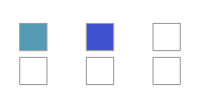
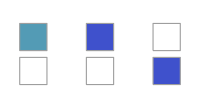
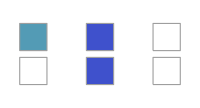
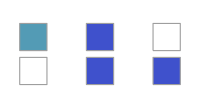
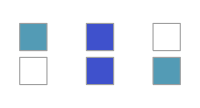
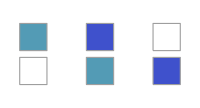
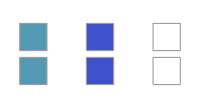
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
urs3=getAllUniqueRules[3,1];
Grid[Partition[RulePlot[CellularAutomaton[{#,3,0}],ColorRules->colorRules,ImageSize->200,PlotLegends->Placed[Subscript[#,3,1], Below]]&/@Keys[urs3],UpTo[4]]]
```

: Sigue el comportamiento de la regla .

: Es una regla con un atractor con periodo 2 pero que no es reversible. Esta regla guarda cierta similitud con  por tener un atractor periodico.

: Esta regla tiene 2 atractores de punto fijo. Esta regla guarda cierta similitud con .

: Esta regla tiene 1 atractor de punto fijo. Esta regla guarda cierta similitud con .

: Esta regla tiene 1 atractor periodico y 1 atractor de punto fijo. Por lo que guarda similitud con las reglas  y .

: La regla  tiene el mismo comportamiento que , pues es un atractor cuyo periodo se define por el numero de estados y el mismo es la regla inversa.

: La regla  tiene  el mismo comportamiento que , pues es un atractor constante con periodo de 1 y es la inversa de si mismo.

Hacer el analisis manual resulta exhaustivo y poco practico porque aunque decimos que “guarda similitud” por la forma en como se comporta su atractor, no tenemos una metrica o una forma consistente de definir dichas relaciones, es por eso, que en lugar de explorar mediante un analisis en individual se busca definir una asociación directa entre ellas.

Para realizar las pruebas se utiliza el siguiente elemento iconizado que almacena todos los comportamientos unicos para los primeros 7 estados. Aunque la vecindad sea 1, aun existen  reglas, por lo que el calculo crece exponencialmente.

```mathematica
urs=;
```

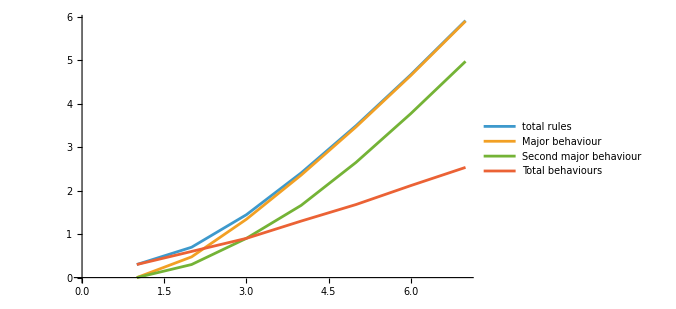

```mathematica
ListLinePlot[
Transpose[MapThread[{#1^#1,#2[[-1,1]],If[Length[#2]>=2,#2[[-2,1]],0],Length[#2]}&,{Range[7],urs}]],
ScalingFunctions->"SignedLog",
PlotLegends->{"total rules","Major behaviour","Second major behaviour","Total behaviours"},
ImageSize->500
]
```

A continuación, se muestran las reglas agrupadas por numeros de estados. Podemos observar que que todas todas las reglas de  estados son un subconjunto de las reglas con  estados, con la diferencia de que al nuevo estado se le asigna una transición a 0 (el primer estado).

```mathematica
burs=Table[IntegerDigits[#,Max[2,i],i]&/@urs[[i,;;,1]],{i,1,Length[urs]}];
Module[{cell=10,maxRows=50},
Grid[{With[{nrows=Min[maxRows,Dimensions[#][[1]]],
ncols=Dimensions[#][[2]]},
ArrayPlot[#[[;;UpTo[maxRows]]],
ColorRules->colorRules,
Mesh->True,
PlotRangePadding->0,
ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},
ImageSize->{cell*ncols,cell*maxRows}]]&/@burs
},Spacings->{2, 0}]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

La primer hipotesis es que existia una una forma de generar toda esa secuencia mediante un algoritmo o una formula, y depues existia una función que extraia unicamente las reglas que pertenecian a ese espacio. Esto no se pudo demostrar ya que la secuencia generada es aleatorio o almenos no se pudo encontrar una patrón universal, sino unicamente patrones aislados. Resulta interesante como dentro de la misma definición de los automatas celulares podemos encontrar estas formas complejas.

La siguiente hipotesis era que existe un mapeo entre las reglas que nos permite movernos entre espacios de CAs. Es decir, nosotros podemos movernos de la regla  a la  unicamente añadiendo un nuevo estado que apunte al estado 0. Pero surge la pregunta, ¿Tienen todos el mismo comportamiento? Vamos a mostrar las evoluciones para unos ejemplos.

Reglas {0,0,0,0,0,0,0}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,0}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Reglas {0,0,0,0,0,0,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,1}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Reglas {0,0,0,0,1,1,2}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,2}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

Reglas {0,0,0,0,1,1,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,1}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics-

Observamos que el comportamiento es practicamente el mismo, pues el ultimo estado unicamente realizando una llamada al primero. Por lo que inferimos 2 cosas de aqui. Si la regla  es reversible, la regla  no lo es, donde x y  tienen el mismo vector de regla. 
Ahora, si nosotros podemos aplicar la función de añadir un nuevo con transición el elemento vacio, tambien debe de ser posible de realizar el proceso inverso, es decir, a una regla cuyo ultimo estado tenga una transición al 0 puede ser eliminida siempre y cuando ningún otro estado tenga una transición al ultimo estado. Esto se cumple para los ejemplos ya mostrados, por lo que estamos haciendo es movernos entre los subconjuntos del espacio de reglas. Pero existen casos excepcionales que no parecen cumplir con esto, por ejemplo, la regla , que si le quitamos las ultimas transiciones obtenemos las siguientes reglas:

```mathematica
Grid[{Module[{cas={CellularAutomaton[{31,5,0},Range[4,0,-1],5],CellularAutomaton[{21,4,0},Range[3,0,-1],5],CellularAutomaton[{13,3,0},Range[2,0,-1],5]},labels={Subscript[31,5,1],Subscript[21,4,1],Subscript[13,3,1]},cell=30},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},MapThread[With[{nrows=Dimensions[#1][[1]],ncols=Dimensions[#1][[2]]},ArrayPlot[#1,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,PlotLabel->#2,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&,{cas,labels}]]]}]
```

-Graphics-

Pero las reglas  ni  no pertenencen a la lista de comportamientos unicos, sin embargo, podemos aplicar la función InverseRules para encontrar el representante de ese ese comportamiento y descubirir de donde viene here dado ese patrón. Haciendo esto, Descubrimos que la regla  tiene el siguiente patrón aplicando las dos posibles funciones. Este proceso finaliza hasta que no es posible realizar ninguna de las 2 operaciones.

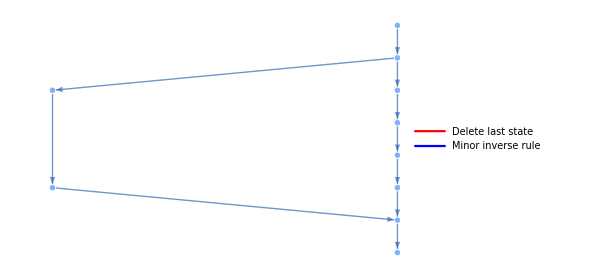

```mathematica
Module[{
vectors={{0,0,1,1,1},{0,1,1,1},{1,1,1},{0,0,0},{0,0},{0},{0,0,2,0},{0,2,0},{0,1,1},{1,1}},
edges={{0,0,1,1,1}->{0,1,1,1},{0,1,1,1}->{1,1,1},{1,1,1}->{0,0,0},{0,0,0}->{0,0},{0,0}->{0},{0,1,1,1}->{0,0,2,0},{0,0,2,0}->{0,2,0},{0,2,0}->{0,1,1},{0,1,1}->{1,1},{1,1}->{0,0}},
colores={({0,0,1,1,1}->{0,1,1,1})->Red,({1,1}->{0,0})->Blue,({0,1,1,1}->{1,1,1})->Red,({0,0,0}->{0,0})->Red,({0,0}->{0})->Red,({0,0,2,0}->{0,2,0})->Red,({0,1,1}->{1,1})->Red,({1,1,1}->{0,0,0})->Blue,({0,1,1,1}->{0,0,2,0})->Blue,({0,2,0}->{0,1,1})->Blue}},
Legended[LayeredGraph[
Graph[
edges,
EdgeStyle->colores,
VertexShapeFunction->(Inset[
ArrayPlot[{#2},
ColorRules->colorRules,
ImageSize->{Length[#2]*20,20},
Mesh->True,
MeshStyle->Gray,
ImagePadding->0,
PlotRangePadding->0
],#1]&),
VertexSize->{0.01,0.25}],
ImageSize->{450,Automatic}
],LineLegend[colores[[All,2]],{"Delete last state","Minor inverse rule"}]]
]
```

Podemos replicar este proceso para cualquier regla, sin importar el numero de estados, a continuación se muestran algunos ejemplos para diferentes numeros de estados.

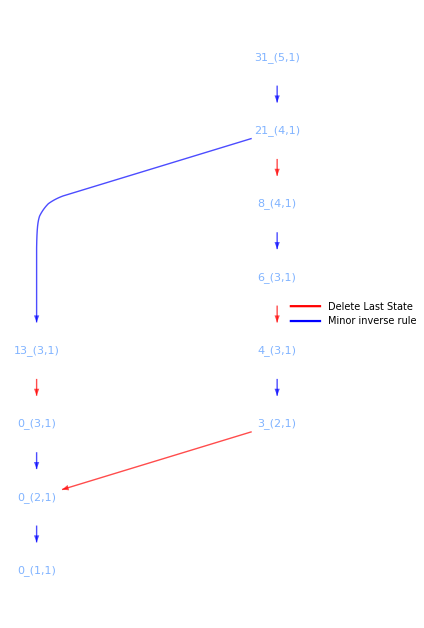
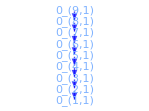
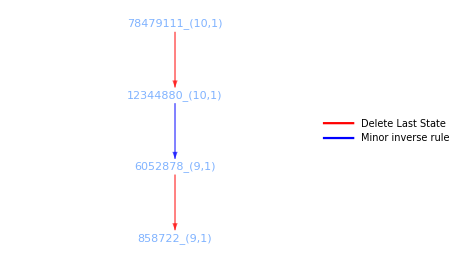
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{rulialGraph[getTransitions[{31,5,0}]],
rulialGraph[getTransitions[{0,9,0}]],
rulialGraph[getTransitions[{78479111,10,0}]]
}}]
```

A continuación se muestra el hipergrafo de todas las relaciones existentes. Cada nota contiene a toras las reglas con el mismo comportamiento, son los elementos que comparten la malla. La altura representa el numero de estados y las flechas hacia abajo apuntan a la regla de la cual imitan el comportamiento. Como ya se habia demostrado, existen reglas que no heredan de otras, es decir, que su comportamiento es unico. Con esto, ademas de reducir significamente el numero de comportamientos al añadir mas estados, tambien se muestran las relaciones de comportamiento.

```mathematica
Import["./trans_0d.pdf"][[1]]
```

-Graphics-

Vamos a generar el grafo que contenga todas estas conexiones. Aunque tecnicamente la mejor definición es un hypergrafo es una función que no se encuentra bien optimizada en Mathematica. Este grafo va a acontener todas las relaciones de 5 estados. Y va a atener la nomenclatura propuesta. Si en algun punto es necesario actualizar la nomenclatura a la dimensión unicamente sera necesario añadir otro subindice a todos estos elementos, nada complicado. 
Ahora bien, este grafo tiene que tener todas las relaciones: inversas, espejo y reducción de estados:

```mathematica
edge={};
edgeStyle={};
```

```mathematica
s=3;
n=1;
rules=Subscript[#,s,n]&/@Range[0,s^(s^n)-1];
{edge,edgeStyle}=addData[rules,edge,edgeStyle];
```

```mathematica
g=Graph[edge,EdgeStyle->edgeStyle];
```

```mathematica
WeaklyConnectedGraphComponents[reduce[g]][[1]]
```

$Aborted

## One Dimensional CA

Hasta el momento solo hemos visto autoamtas celulares adfimensionales. Tecnicamente, no solo autoamtas celulares sino simples maquinas de estados. Ahora, vamos a iniciar aumentando la dimensionalidad. Para esto, podemos iniciar con la configuración mas simple de un automata celular de una dimensión. Imaginemos una linea infinita de celulas, pero cuya vecindad esta definida por un unico elemento.  Este no necesariamente tiene que ser el mismo, pero todas estas configuraciones tienen las propiedades heredadas de un CA adimensional. La información solo considera un estado. Esta propiedad de tener un solo vecino vemos que se hereda en combinaciones futuras, pero eso ser vera continuación.
Otra cosa, si utilizamos un unico estado, no importa el numero de vecinos que tengamos, porque todos tendran la misma regla: , por lo que nuevamente, es la regla absoulta. Por el momento, podemos seguir utilizando la misma nomenclatura .

```mathematica
CaRulePlot[{0,1,1/2}]
```

-Graphics-

Podemos iniciar con las asociaciones aunque sean triviales. En esta regla, podemos ignorar el estado de la izuiqerda o el de la derecha y tenemos el mismo comportamiento. Por lo que la transición no depende de ninguno de los estados. ¿Podemos decir que la regla  proviene de ?

Ahora si, vamos a ver el comportamiento con 2 estados y dos vecinos, la primer configuracion en una dimension con comportmaiento no trivial:

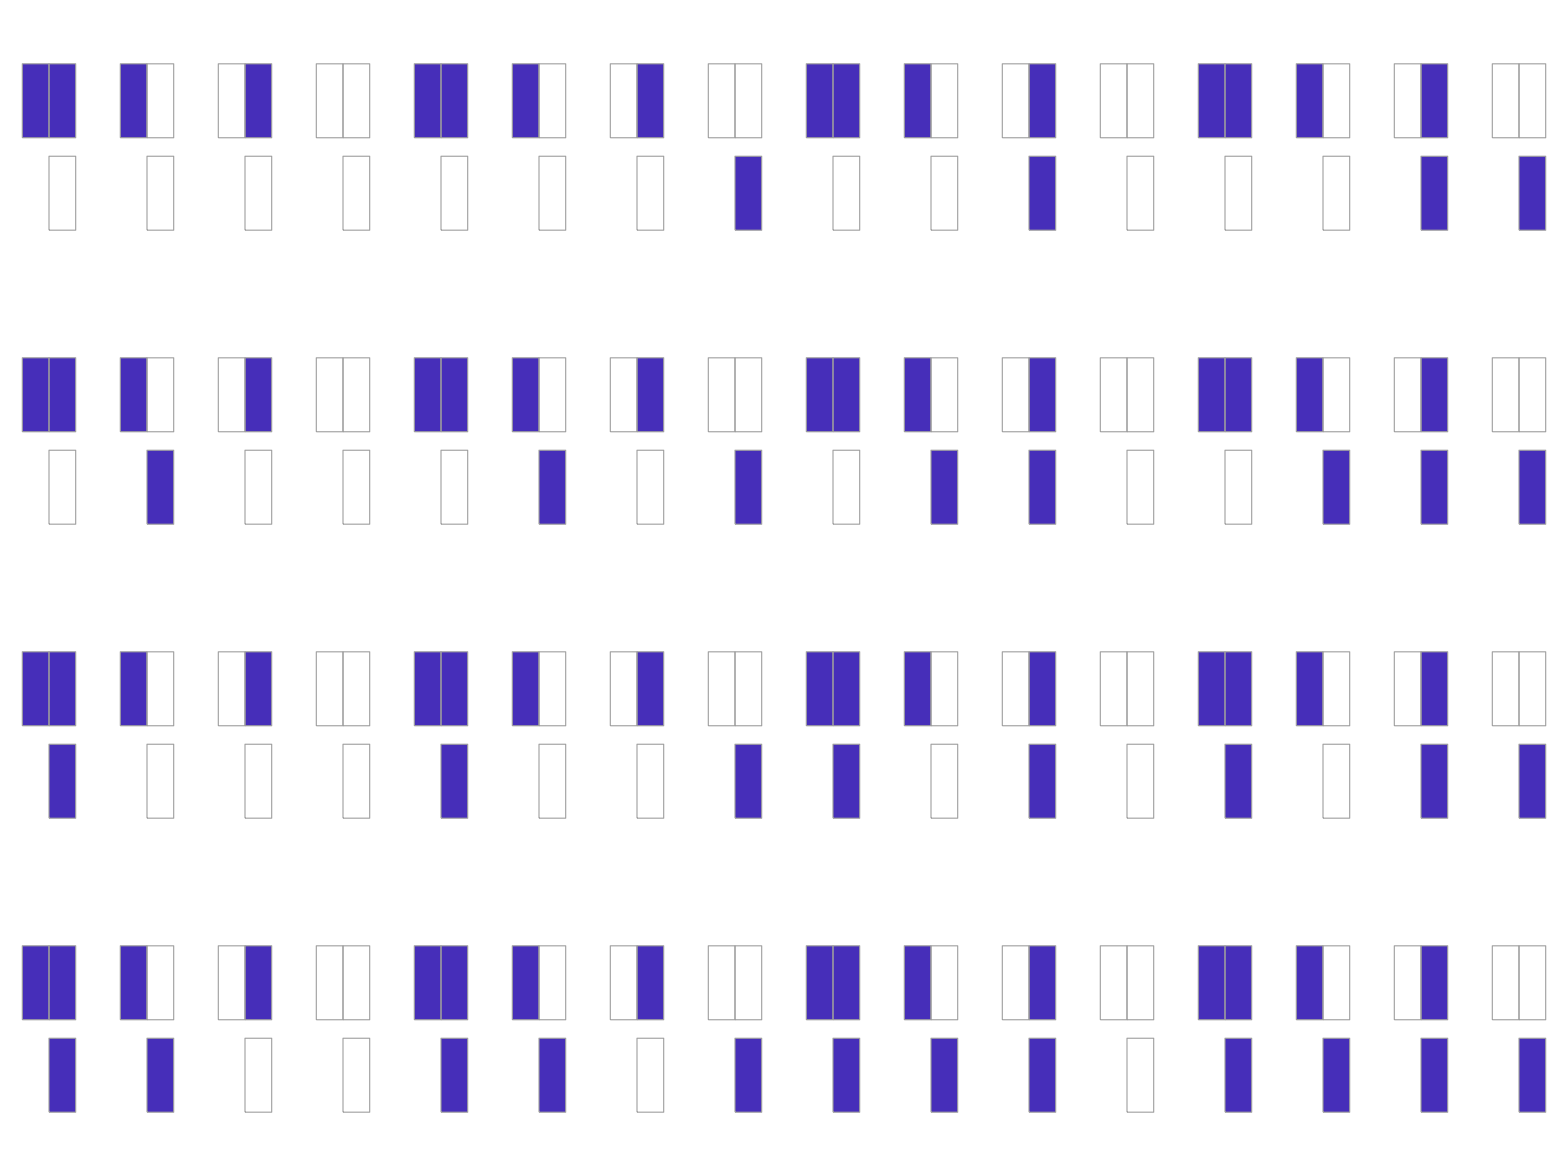

```mathematica
Grid[Partition[CaRulePlot[{#,2,1/2}]&/@Range[0,2^2^2-1],4]]
```

Al igual que antes, podemos encontrar ciertas relaciones que iremos descartando de manera manual y despues de forma algoritmica. A diferencia de antes que no teniamos una base, ahora podemos aplicar ciertos filtros, el primer es encontrar las reglas que pertenecen a CA adimensionales. Primero restringimos el numero de ellos buscando las permutaciones de estados:

{0→{0,15},1→{1,7},2→{2,11},3→{3},4→{4,13},5→{5},6→{6,9},8→{8,14},10→{10},12→{12}}

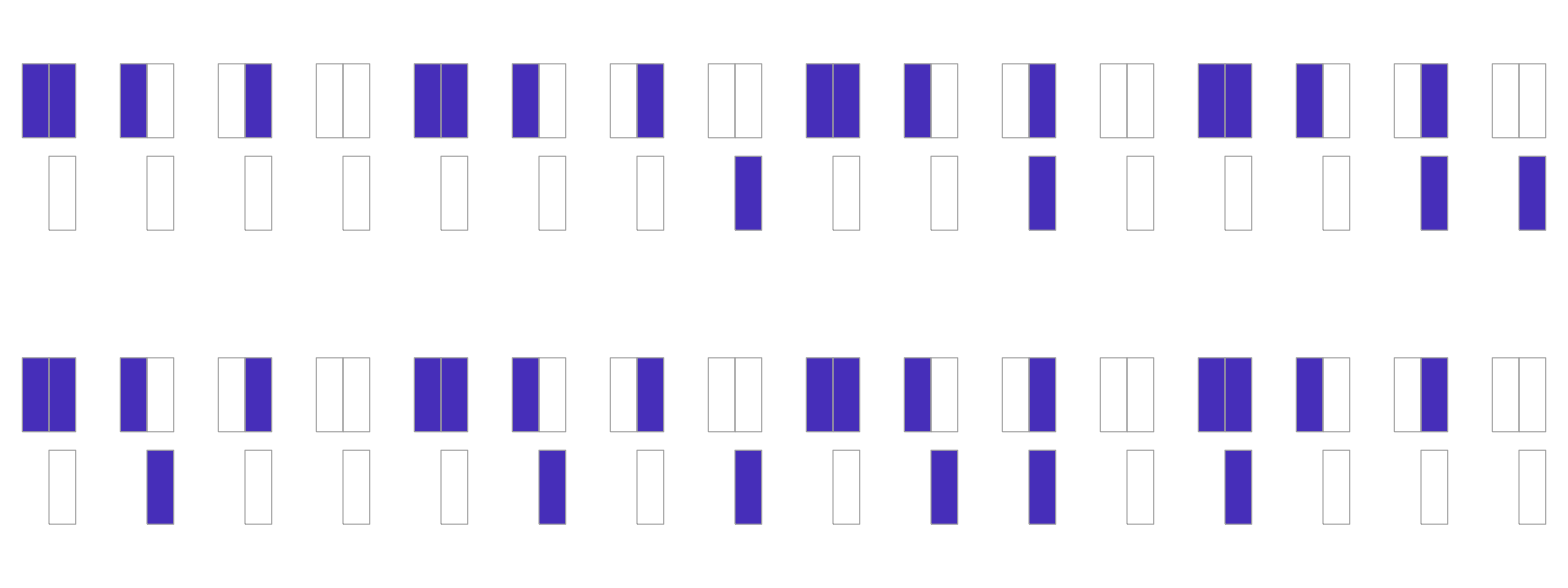

```mathematica
assoc=#[[1]]->#&/@DeleteDuplicates[InverseRules[{#,2,1/2}]&/@Range[0,15]]
Grid[Partition[CaRulePlot[{#[[1]],2,1/2}]&/@assoc,4]]
```

Ahora, necesitamos una función additional, porque los CA adimensionales son simetricos, pero aqui tenemos reglas como las siguientes, cuyo comportamiento se encuentra invertido:

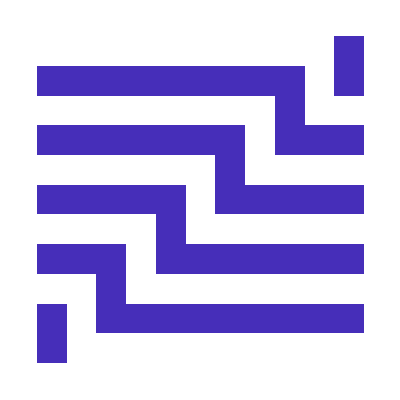
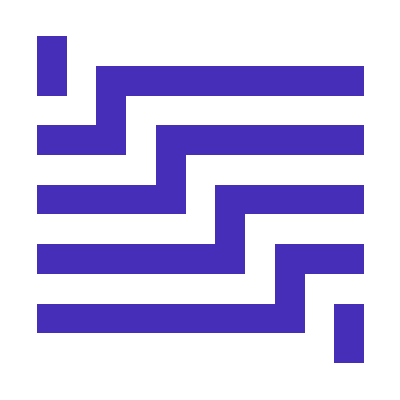
-Graphics- | -Graphics-

```mathematica
init={{1},0};
Grid[{{
RulePlot[CellularAutomaton[{3,2,ReverseSort[{{0},{1}}]}],init,10,PlotLegends->"Text",ColorRules->colorRules],
RulePlot[CellularAutomaton[{5,2,ReverseSort[{{0},{-1}}]}],init,10,PlotLegends->"Text",ColorRules->colorRules]}
}]
```

Sin embargo, para el notebook de Mathematica es necesario tambien hacer un cambio, y es definir la vecindad manualmente, porque tradicionalemnte se escribe como CellularAutomaton[{3,2,1/2}] pero la vecindad tambien tiene que ser invertida, es decir, ya no se toma el lado izquierdo, se toma el lado derecho, osea que los vectores de desplazamiento se invierten y se reorden. Lo que antes era una vecindad definida por {{1},{0}}, en el espejo se cambia por {{0},{-1}}. Sin embargo, al filtrar los espejos podemos seguir utilizando la definición tradicional, pues esos elementos no forman parte de eso. Ademas de las permutaciones de colores de estados, ahora tambien nos interesa agrupar todas aquellas reglas que son sus equivalentes en espejos. A lo mucho, solo puede tener un espejo, porque hay comportamientos que ya son simetricos. Por lo que de 16 reglas, reducimos a tan solo 7 comportamientos unicos:

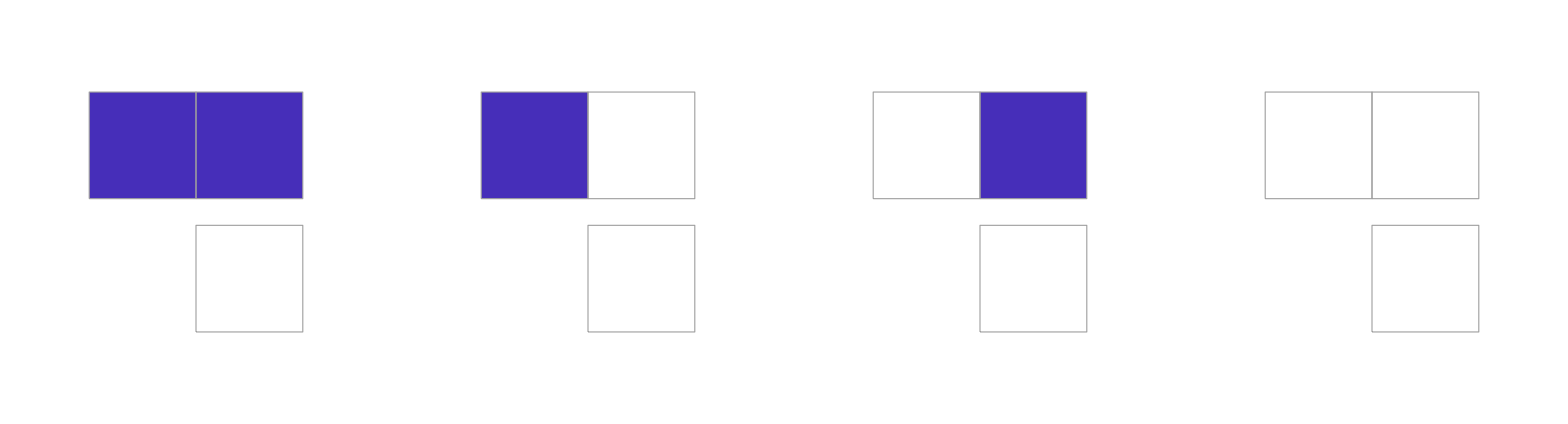
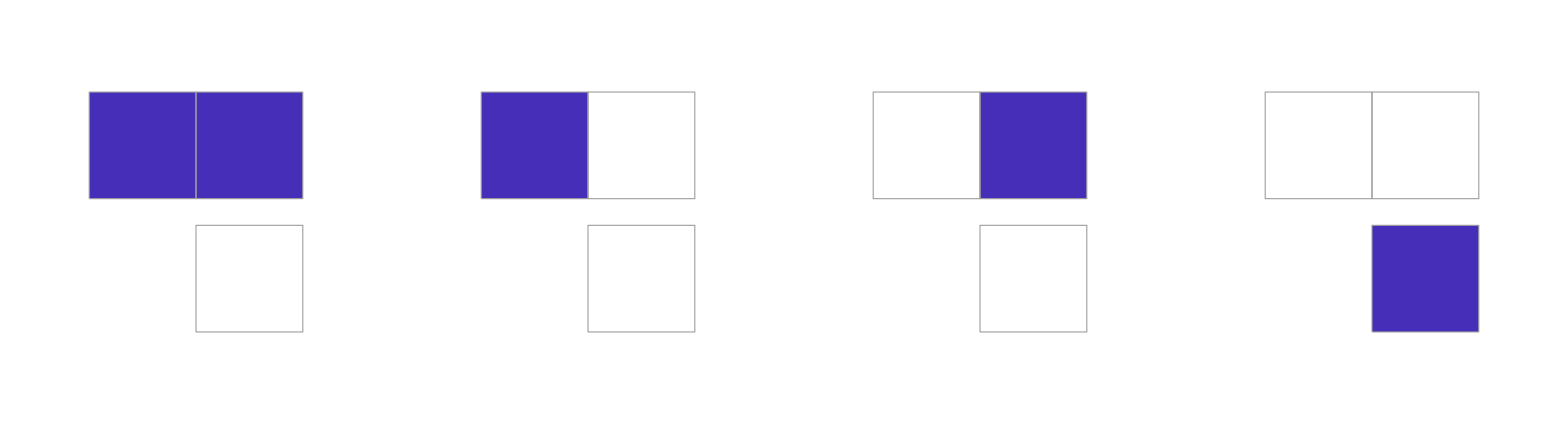
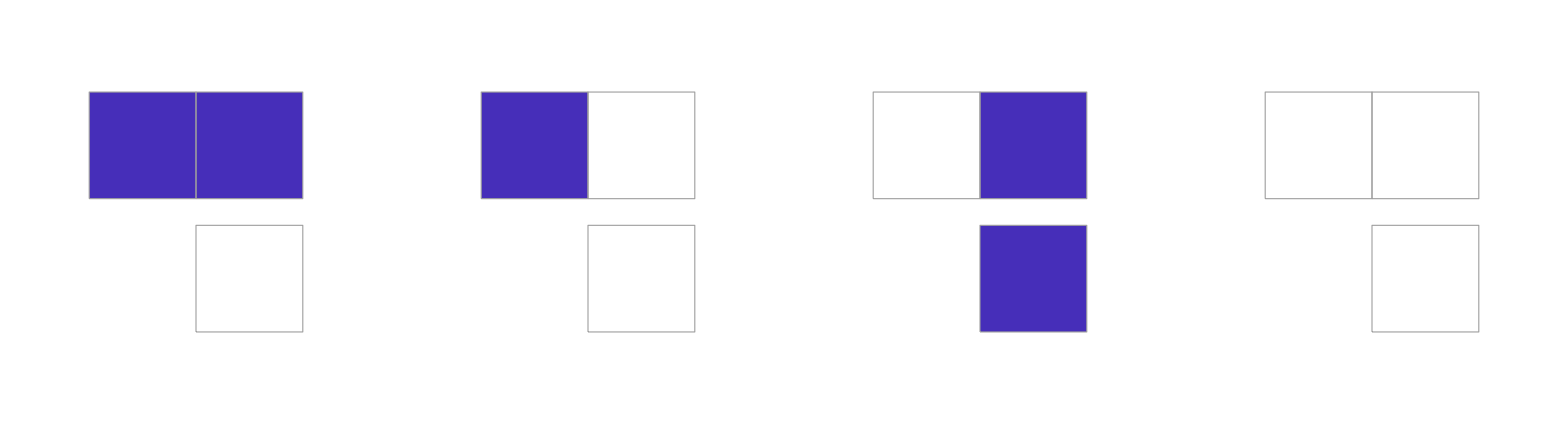
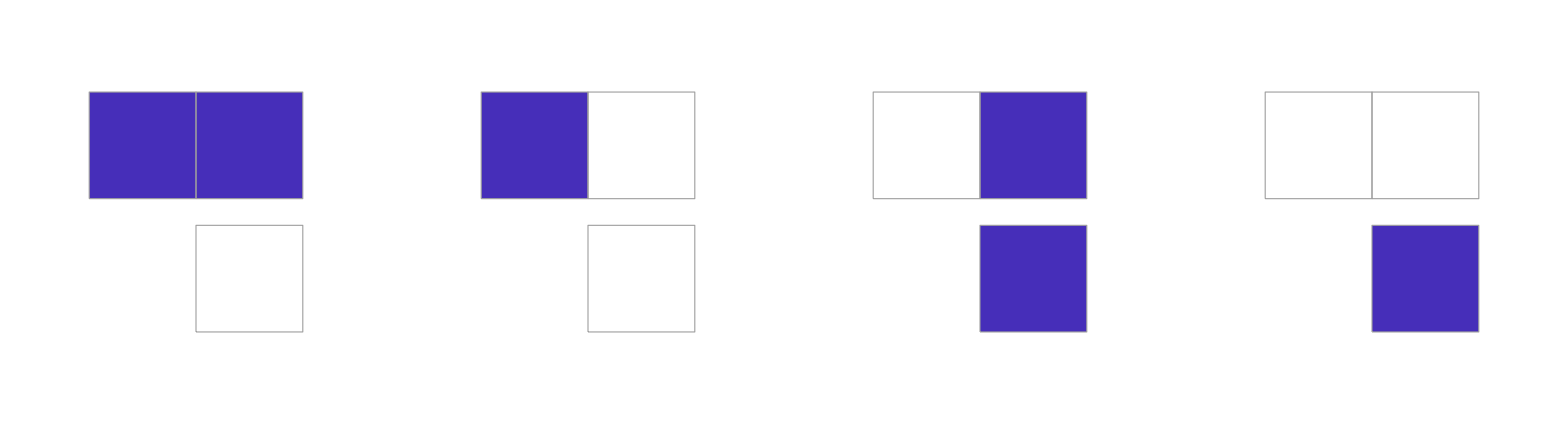
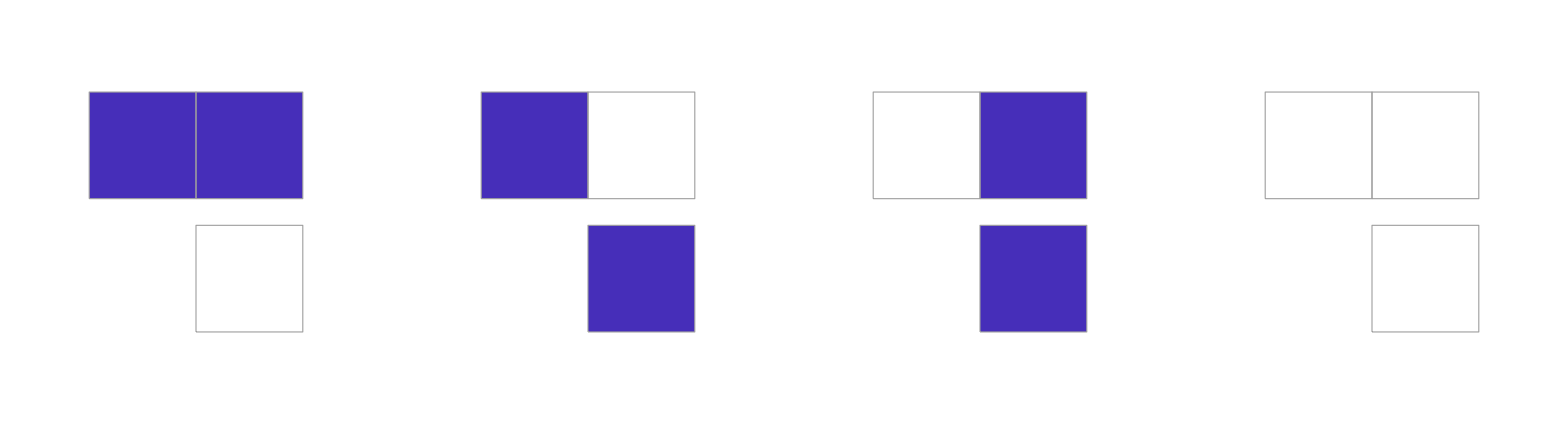
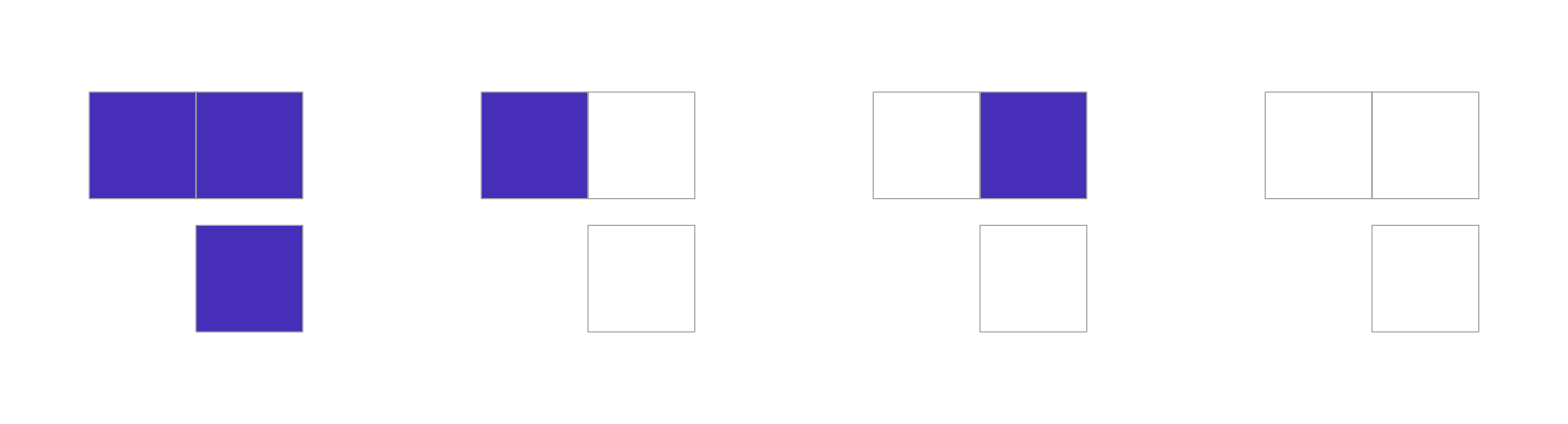
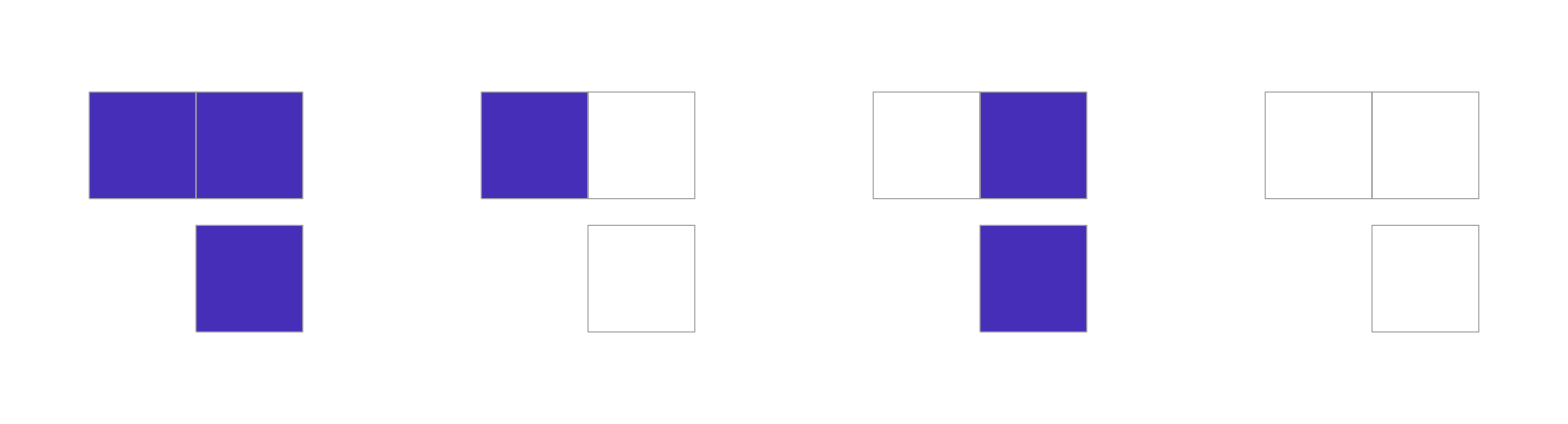
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
#[[1]]->MirrorRules[{#[[1]],2,1/2}]&/@assoc;
Grid[Partition[CaRulePlot[{#,2,1/2}]&/@{0,1,2,3,6,8,10},UpTo[4]]]
```

De estos comportamientos, encontramos 3 relaciones con configuraciones previas.

La regla  no depende de ninguno, al igual que  y

La regla  unicamente depende del vecino de la izquierda, por lo que imita a la regla

La regla  unicamente depende del vecino de la derechoa, por l oque imita a la regla

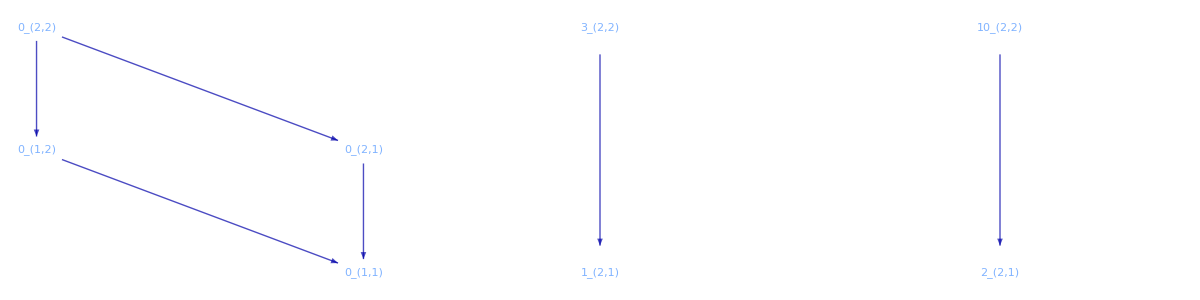

```mathematica
Grid[{{rulialGraph[{{0,2,1/2}->{0,1,1/2},{0,1,1/2}->{0,1,0},{0,2,1/2}->{0,2,0},{0,2,0}->{0,1,0}}],
rulialGraph[{{3,2,1/2}->{1,2,0}}],
rulialGraph[{{10,2,1/2}->{2,2,0}}]}}]
```

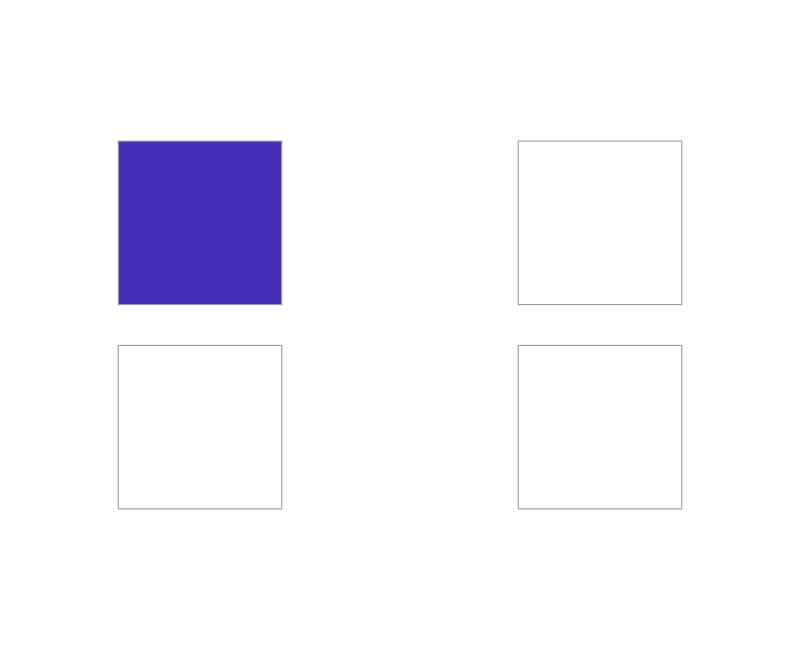

```mathematica
CaRulePlot[{0,2,0}]
```

Las evoluciones de las reglas  y  son exactamente iguales. Para la regla  y  hay que considerar que es el inverso de la celula a la izquierda, por lo que si trasladamos los bloques, a la izquierda, encontramos el mismo comportamiento.

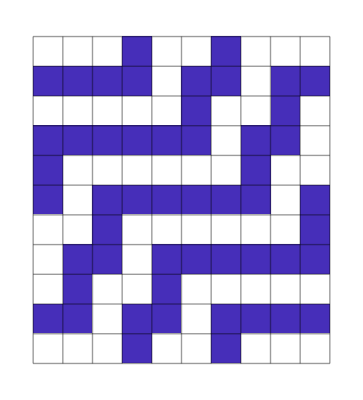
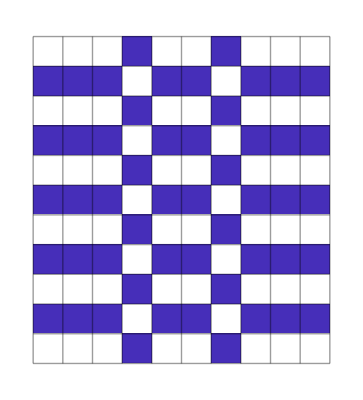
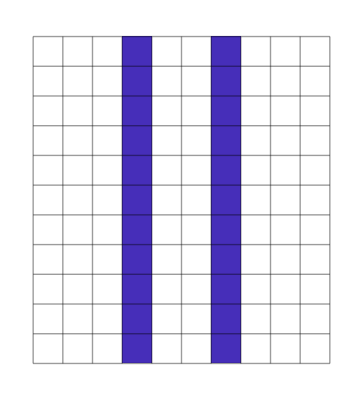
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
init={0,0,0,1,0,0,1,0,0,0};
Grid[{RulePlot[CellularAutomaton[#],init,10,PlotLegends->"Icon",ColorRules->colorRules,Mesh->True]&/@{{3,2,1/2},{1,2,0},{10,2,1/2},{2,2,0}}
}]
```

Al final, tenemos solo 4 comportamientos unicos:

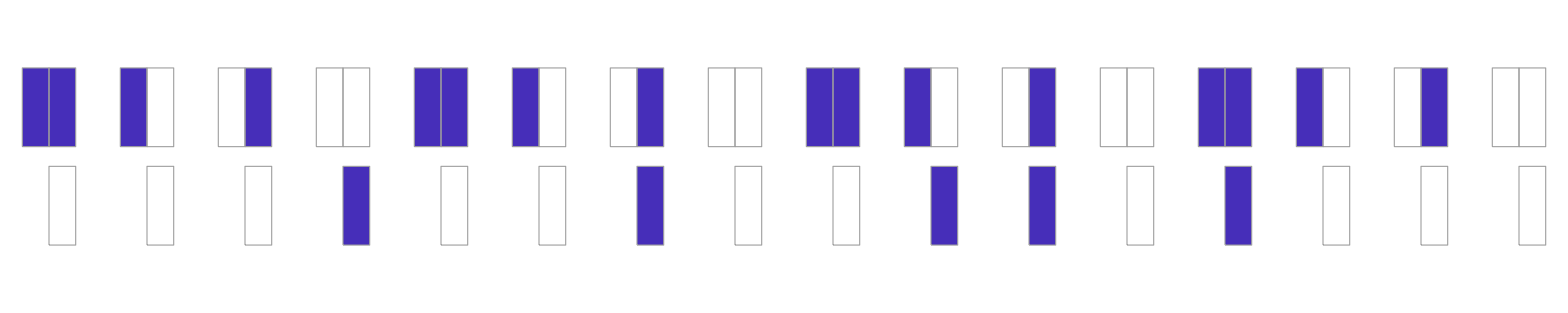

```mathematica
Grid[{CaRulePlot[{#,2,1/2}]&/@{1,2,6,8}}]
```

Con semillas aleatorias, encontramos los siguientes comportamientos, ninguna de ellas es reversible.

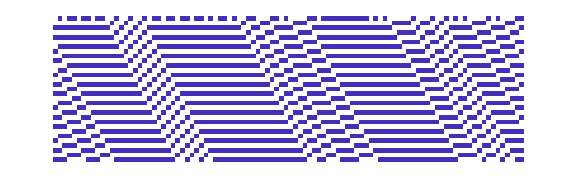
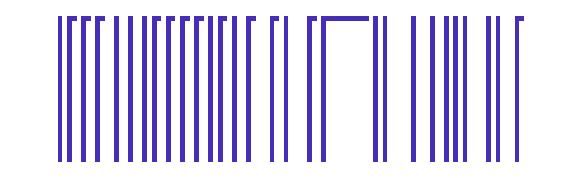
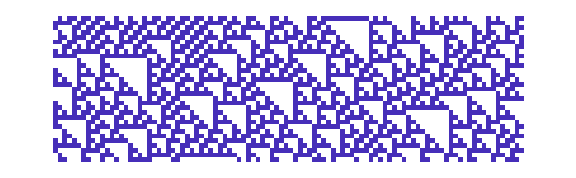
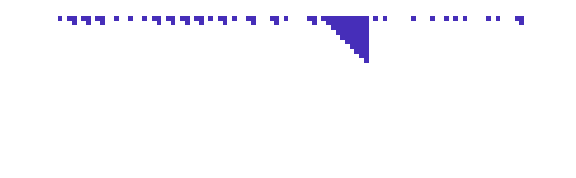
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
init=RandomInteger[{0,1},100];
Grid[Partition[RulePlot[CellularAutomaton[{#,2,1/2}],init,30,ColorRules->colorRules,ImageSize->Large,PlotLegends->"Icon"]&/@{1,2,6,8},2]]
```

Podemos aumentar el numero de estados y la vecindad, si aumentamos la vecindad finalmente llegariamos a los ECA. Si aumentamos el numero de estados, tendremos que encontrar la relación de las nuevas reglas y buscar si existe algun comportamiento similar al que ocurre cuando aplicamos la reducción de estudios.
Ahora vamos a empezar a analizar 3 estados con 2 vecinos, algo que no he visto ni probado antes, esta primera vez puede ser lo complicado por lo que puede uqe lo haga un poco mas lento, pero pues ni modo jaja.

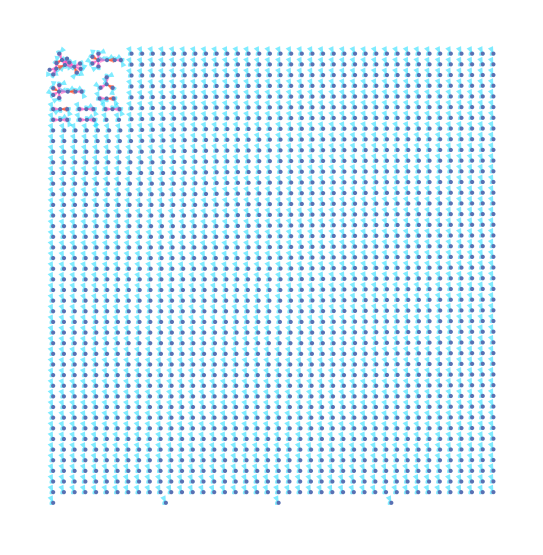
```mathematica
a=-Graphics-;
```

```mathematica
graphs=WeaklyConnectedGraphComponents[a,Subscript[0,1,1]];
```

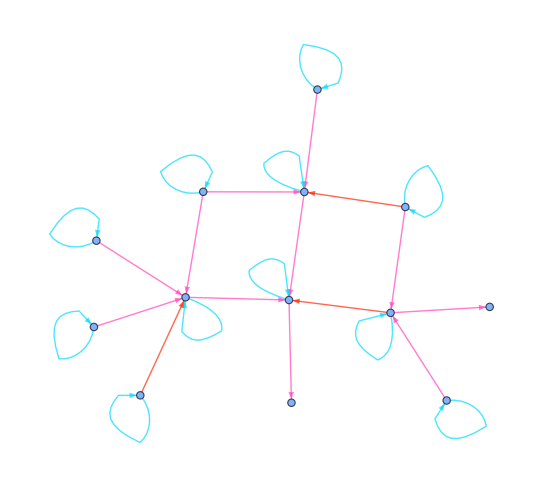

```mathematica
GraphPlot[graphs[[1]],GraphLayout->"SpringEmbedding"]
```

```mathematica
unknown=Select[graphs,Length[VertexList[#]]==1&];
```

```mathematica
urls=Sort@Flatten[Select[VertexList[#]&/@unknown,#[[1,2]]==3&]];
```

```mathematica
CaArrayPlot[urls[[1]],RandomInteger[{0,1},100],10]
```

CaArrayPlot[5_(3,2),{0,1,1,0,1,0,0,1,1,1,1,1,1,0,1,1,1,0,1,1,1,1,1,0,1,0,0,0,0,1,0,1,0,0,1,1,0,1,1,0,1,0,0,0,0,0,1,0,0,1,1,0,0,1,1,0,1,0,1,0,1,1,1,0,0,1,1,1,1,1,1,1,0,0,1,0,0,0,1,1,1,0,0,0,0,1,1,1,0,0,1,0,1,0,0,1,0,0,1,0},10]

```mathematica
seed=RandomInteger[{0,2},200];
```

```mathematica
Manipulate[{CaArrayPlot[urls[[i]],seed,100],urls[[i]],CaRulePlot[urls[[i]]]},{i,1,Length[urls],1}];
```

```mathematica
graphs=WeaklyConnectedGraphComponents[a];
```

```mathematica
unknown=Select[graphs,Length[VertexList[#]]==1&];
```

```mathematica
urls=Sort@Flatten[Select[VertexList[#]&/@unknown,#[[1,2]]==3&]];
```

```mathematica
seed=RandomInteger[{0,2},20];
```

```mathematica
Manipulate[Grid[Transpose@{{CaArrayPlot[urls[[i]],seed,10],urls[[i]],CaRulePlot[urls[[i]]]},
{CaArrayPlot[Subscript[1,2,2],ReplaceAll[seed,2->1],10],Subscript[1,2,2],CaRulePlot[Subscript[1,2,2]]}
}],{i,1,Length[urls],1}]
```

```mathematica
b=Subscript[67,3,2];
c=Subscript[68,3,2];
d=Subscript[40,3,2];
e=Subscript[80,3,2];
e41=Subscript[41,3,2];
e43=Subscript[43,3,2];
e44=Subscript[44,3,2];
e49=Subscript[49,3,2];
Grid[Transpose@{
{CaArrayPlot[d,seed,20],d,CaRulePlot[d]},
{CaArrayPlot[e41,seed,20],e41,CaRulePlot[e41]},
{CaArrayPlot[e43,seed,20],e43,CaRulePlot[e43]},
{CaArrayPlot[e44,seed,20],e44,CaRulePlot[e44]},
{CaArrayPlot[e49,seed,20],e49,CaRulePlot[e49]},
{CaArrayPlot[c,seed,20],c,CaRulePlot[c]},
{CaArrayPlot[b,seed,20],b,CaRulePlot[b]},
{CaArrayPlot[e,seed,20],e,CaRulePlot[e]}
}]
```

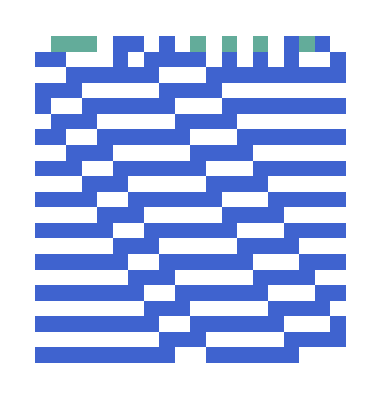
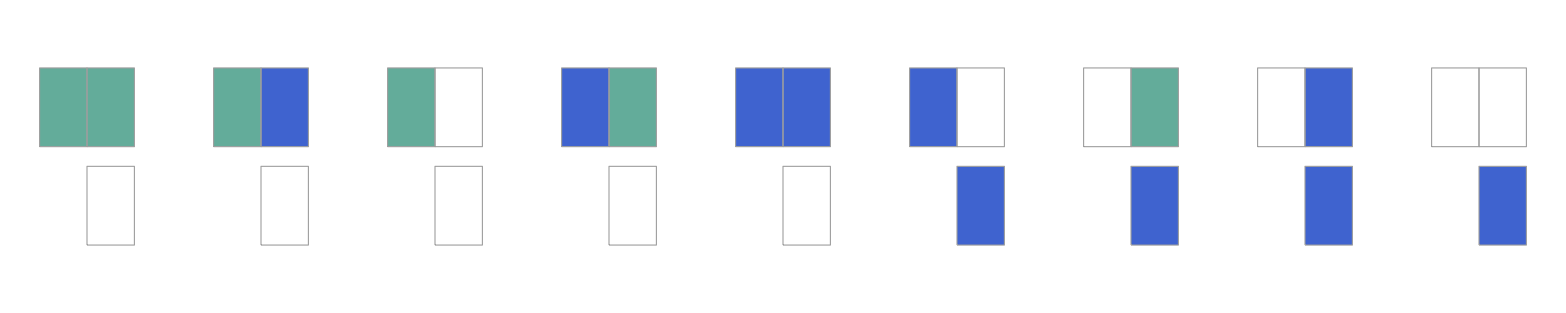
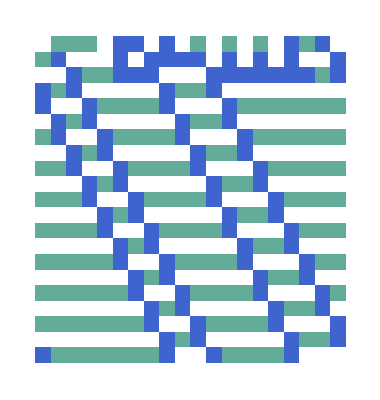
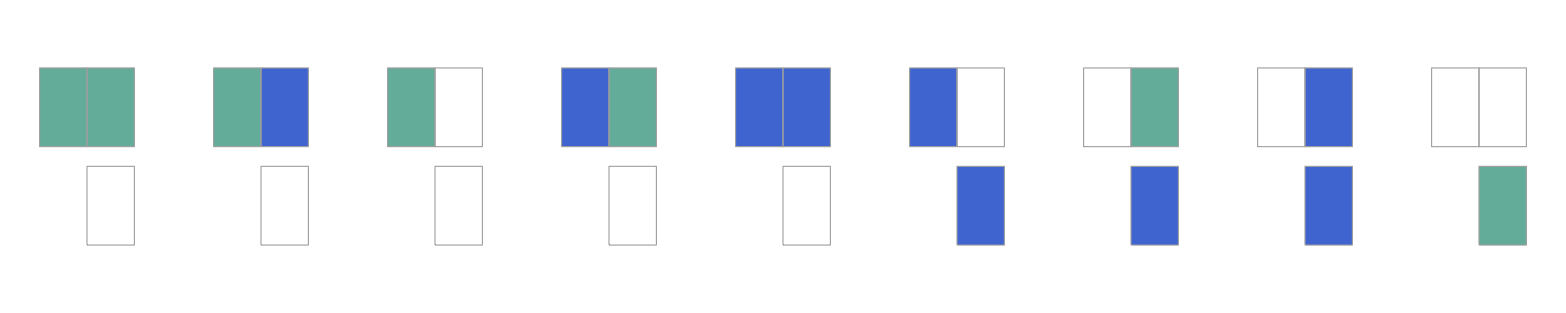
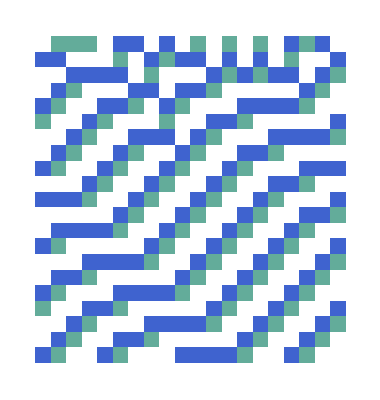
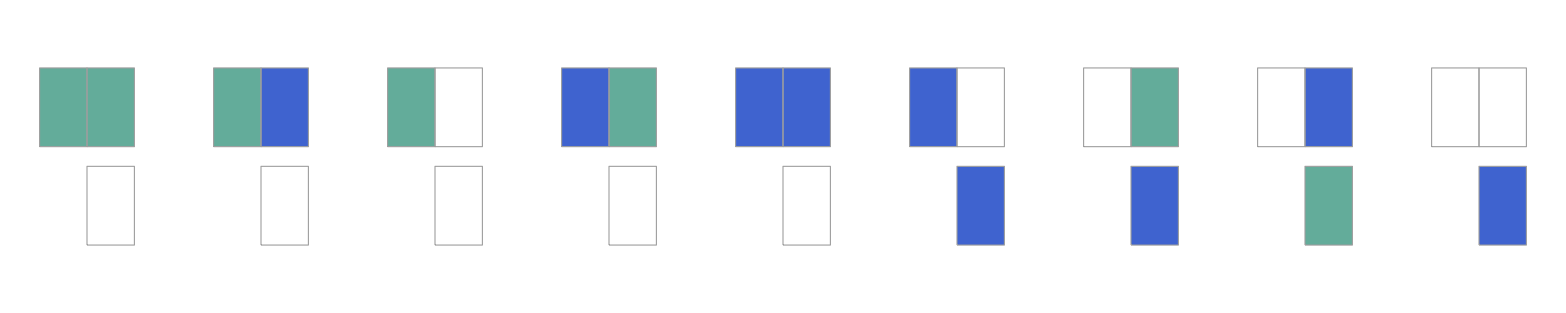
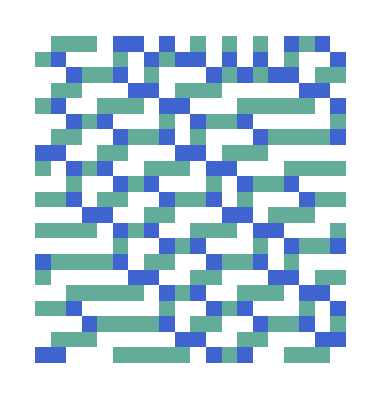
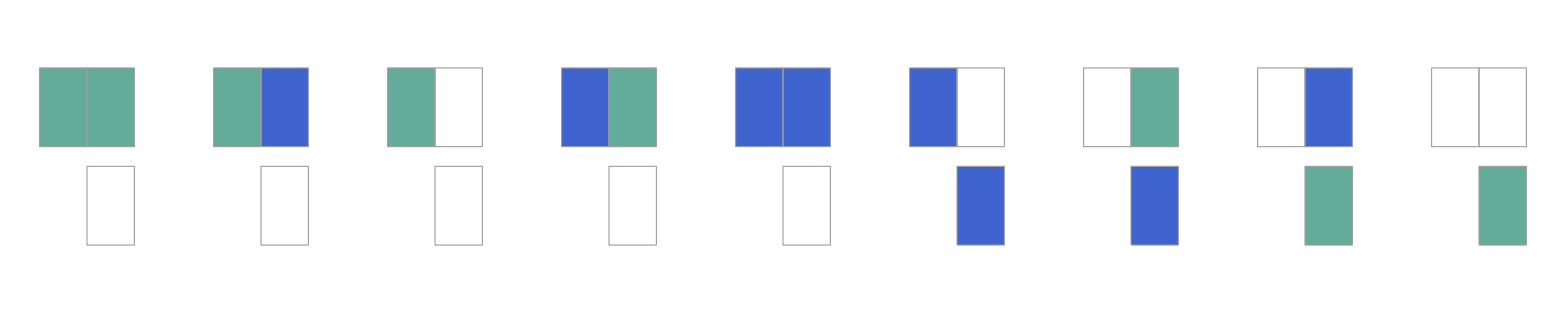
{{-Graphics-,40_(3,2),-Graphics-},{-Graphics-,41_(3,2),-Graphics-},{-Graphics-,43_(3,2),-Graphics-},{-Graphics-,44_(3,2),-Graphics-},{-Graphics-,49_(3,2),-Graphics-},{-Graphics-,50_(3,2),-Graphics-},{-Graphics-,52_(3,2),-Graphics-},{-Graphics-,53_(3,2),-Graphics-},{-Graphics-,67_(3,2),-Graphics-},{-Graphics-,68_(3,2),-Graphics-},{-Graphics-,70_(3,2),-Graphics-},{-Graphics-,71_(3,2),-Graphics-},{-Graphics-,76_(3,2),-Graphics-},{-Graphics-,77_(3,2),-Graphics-},{-Graphics-,79_(3,2),-Graphics-},{-Graphics-,80_(3,2),-Graphics-}}

```mathematica
r=Subscript[FromDigits[Join[{0,0,0,0,0},#],3],3,2]&/@Tuples[{1,2},4];
{CaArrayPlot[#,seed,20],#,CaRulePlot[#]}&/@r
```

```mathematica
-Graphics-,Subscript[40, 3,2],-Graphics-
```

Vamos a analizar los patrones inutilizados. Son patrones que unicamente pueden aparecer en las condiciones iniciales y que despues nunca puede ser generados por esa regla. Para trabajar con esta nueva hipotesis trabajaremos con la regla .

```mathematica
r=Subscript[40, 3,2];
CaRulePlot[r]
```

-Graphics-

Podemos asummir que los patrones que quedan inutilziados son aquellos que contiene el estado 2, porque esta regla no genera este estado. Por lo que unicamente nos interesan 4 patrones. Por ejemplo, existe la posibilidad de que se encuentre {0,0} en cualquier parte de una evolución futura?? Para esto tenemos que encontrar las configuraciones iniciales que pueden producir un 0 a la izquierda, las cuales:

```mathematica
{{2,2},{2,1},{2,0},{1,2},{1,1}};
```

y de estas, ahora necesitamos crear otro 0, pero como primer elemento tiene que tener el ultimo elemento de los patrones posibles:

```mathematica
is={{2,2,2},{2,1,2},{1,2,2},{1,1,2}};
```

Si evolucionamos esos sitemas, vemos que podemos encontrar el patrón buscado de {0,0}. por lo que confirmamos que ese patrón es generado.

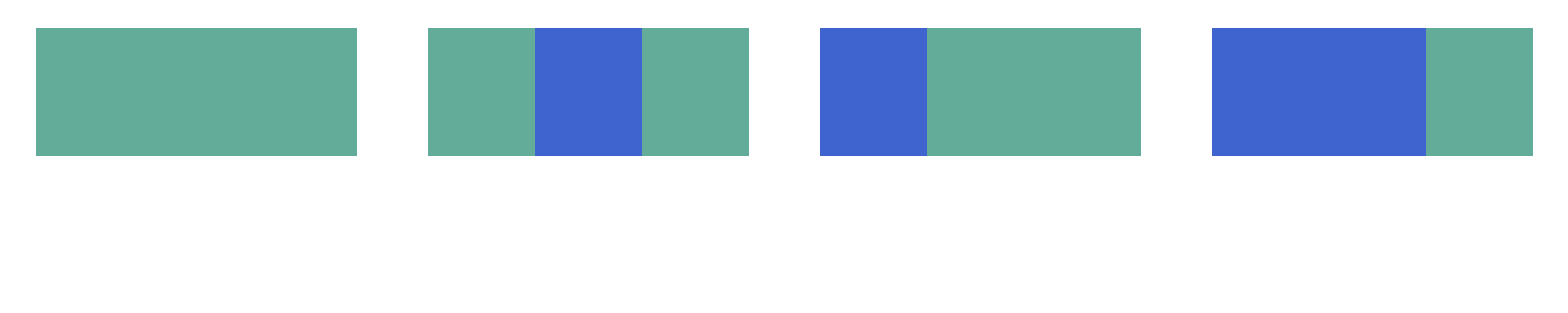

```mathematica
Grid[{CaArrayPlot[r,#,1]&/@is}]
```

Problemos buscando el patrón {2,0} con la regla 68_(3,2):

Estos son los patrones que producen un 2:

```mathematica
{0,0},{1,0}
```

Y esto lo patrones que producen un 0:

```mathematica
{2,2},{2,1},{2,0},{1,2},{1,1}
```

Si hacemos el overlap, vemos que no existe ninguna coincidencia, en donde el segundo elemento del primero sea el primero de segundo, por lo que es imposible generar ese patrón. Podemos concluir entonces que ese patrón no tiene referencia. Ahora, vamos a definir un algoritmo que nos defina que patrones no son alcanzables, porque puede que esta metrica de regeneración nos indique la similitud entre diferentes reglas. Por ejemplo, 2 reglas que tienen el mismo patrón autoreferencial.

Vamos a seguir probando con estos casos, porque es la primer secuenci uqe s encuentra y la idea es extrapolar esta función para concluir que no es propia de un solo escenario.

```mathematica
r=Subscript[68,3,2];
ruleConnections[r_Subscript]:=Module[{k,n,v,nbhdsFor,tuples},k=r[[2]];n=r[[3]];
v=Reverse@IntegerDigits[r[[1]],k,k^n];
nbhdsFor=Function[val,IntegerDigits[#-1,k,n]&/@Flatten[Position[v,val]]];
tuples=Tuples[Range[0,k-1],2];Sort@Table[pat->Sort@Flatten[Table[{seq,#}&/@Select[nbhdsFor[pat[[2]]],#[[;;n-1]]==seq[[-n+1;;]]&],{seq,nbhdsFor[pat[[1]]]}],1],{pat,tuples}]]
```

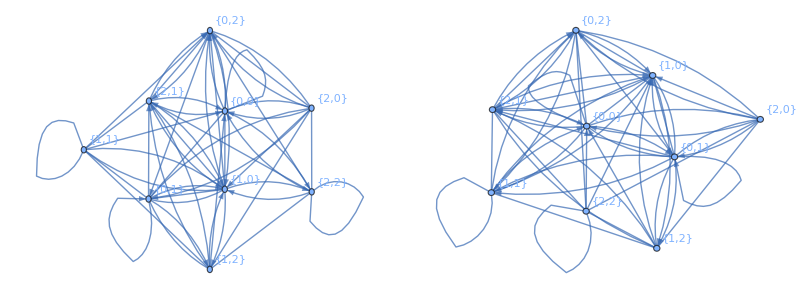

```mathematica
rc=ruleConnections[r];
d=DeleteDuplicates@Flatten@Table[
{#[[1]]->rc[[i,1]],#[[1]]<->#[[2]],#[[2]]->rc[[i,1]]}&/@rc[[i,2]]
,
{i,1,Length[rc],1}
];
g1=Graph[d,VertexLabels->"Name"];
rc=ruleConnections[Subscript[67,3,2]];
d=DeleteDuplicates@Flatten@Table[
{#[[1]]->rc[[i,1]],#[[1]]<->#[[2]],#[[2]]->rc[[i,1]]}&/@rc[[i,2]]
,
{i,1,Length[rc],1}
];
g2=Graph[d,VertexLabels->"Name"];
Grid[{{g1,g2}}]
```

```mathematica
#[[1]]->Length[#[[2]]]&/@ruleConnections[Subscript[40,3,2]]
#[[1]]->Length[#[[2]]]&/@ruleConnections[Subscript[67,3,2]]
#[[1]]->Length[#[[2]]]&/@ruleConnections[Subscript[68,3,2]]
```

{{0,0}→10,{0,1}→5,{0,2}→0,{1,0}→5,{1,1}→7,{1,2}→0,{2,0}→0,{2,1}→0,{2,2}→0}

{{0,0}→10,{0,1}→3,{0,2}→2,{1,0}→5,{1,1}→3,{1,2}→1,{2,0}→0,{2,1}→3,{2,2}→0}

{{0,0}→10,{0,1}→2,{0,2}→3,{1,0}→5,{1,1}→0,{1,2}→1,{2,0}→0,{2,1}→4,{2,2}→2}

```mathematica
s=Subscript[40,3,2]
re=ruleConnections/@InverseRules[s][[;;2]];
#[[1]]->Length[#[[2]]]&/@re[[1]]
#[[1]]->Length[#[[2]]]&/@re[[2]]
```

40_(3,2)

{{0,0}→10,{0,1}→5,{0,2}→0,{1,0}→5,{1,1}→7,{1,2}→0,{2,0}→0,{2,1}→0,{2,2}→0}

{{0,0}→7,{0,1}→0,{0,2}→5,{1,0}→0,{1,1}→0,{1,2}→0,{2,0}→5,{2,1}→0,{2,2}→10}

```mathematica
ruleConnections[Subscript[1,2,2]]
```

{{0,0}→{{{0,1},{1,0}},{{0,1},{1,1}},{{1,0},{0,1}},{{1,1},{1,0}},{{1,1},{1,1}}},{0,1}→{{{1,0},{0,0}}},{1,0}→{{{0,0},{0,1}}},{1,1}→{{{0,0},{0,0}}}}

## Functions

## Prebuilt functions

```mathematica
(*Hay que asociar las reglas*)
cas=Flatten[Table[
u=urs[[i]];
Subscript[#,i,0]&/@#&/@u[[;;,2]]
,{i,1,5}],1];
transitions=DeleteDuplicates[{Subscript@@#[[1]],Subscript@@#[[2]]}&/@Flatten[getTransitions[{#[[1]],#[[2]],#[[3]]}]&/@cas[[;;,1]]]];
```

```mathematica
cas=;
transitions=;
Hypergraph3D[cas,transitions,70,8,1.4];
```

## Functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Definicion de colores*)
inverseColor=RGBColor[0,0.238,1];
mirrorColor=RGBColor[0,0.856,1];
stateColor=RGBColor[1,0.271,0.738];
neighborColor=RGBColor[1,0.148,0.024];
```

```mathematica
addData[rulesIn_List,dataIn_List:{},edgeStyleIn_List:{}]:=Module[
{
data=dataIn,edgeStyle=edgeStyleIn,rules=rulesIn,
inverseRules,mirrorRules,stateRules,neighborRules
},
{inverseRules,mirrorRules,stateRules,neighborRules}=Parallelize[{
DeleteDuplicates@Flatten[Table[Map[rule->#&,InverseRules[rule]],{rule,rules}]],
DeleteDuplicates@Flatten[Table[Map[rule->#&,MirrorRules[rule]],{rule,rules}]],
Select[Map[#->DeleteState[#]&,rules],#[[2]]=!=Null&],
Select[Map[#->DeleteNeighbor[#]&,rules],#[[2]]=!=Null&]}];

data=DeleteDuplicates[Join[data,inverseRules,mirrorRules,stateRules,neighborRules]];
edgeStyle=Join[
edgeStyle,
Thread[inverseRules->Directive[inverseColor,Thick]],
Thread[mirrorRules->Directive[mirrorColor,Thick]],
Thread[stateRules->Directive[stateColor,Thick]],
Thread[neighborRules->Directive[neighborColor,Thick]]];
{data,edgeStyle}
]
```

```mathematica
reduce[g_Graph]:=Module[{blueColors,blueEdgeList,groups,toHead,nodes,reducedEdgeStyle},blueColors={inverseColor,mirrorColor};
blueEdgeList=Cases[edgeStyle,(e_->Directive[Alternatives@@blueColors,___]):>e];
groups=ConnectedComponents[Graph[VertexList[g],blueEdgeList]];
toHead=Dispatch[Flatten[ParallelMap[With[{head=MinimalBy[#,#[[1]]&][[1]]},#->head&/@#]&,groups]]];
reducedEdgeStyle=DeleteDuplicates[edgeStyle/. toHead];
nodes=DeleteDuplicates[reducedEdgeStyle[[;;,1]]];
Graph[nodes,EdgeStyle->reducedEdgeStyle]]
```

#### Inverse Rules

```mathematica
InverseRules[ca_Subscript]:=Module[
{
r=ca[[1]],s=ca[[2]],n=(ca[[3]]-1)/2,
L=ca[[2]]^ca[[3]],outputs,tuples,perms,res
},
outputs=Reverse[IntegerDigits[r,s,L]];(*outputs[[k]]=salida de la vecindad k-1*)
tuples=IntegerDigits[#,s,2n+1]&/@Range[0,L-1];(*tuples[[k]]=vecindad k-1 como n-tupla*)
perms=Permutations[Range[0,s-1]];(*solo s! permutaciones de ESTADOS*)
res=Sort@DeleteDuplicates@Table[
Module[
{pi=AssociationThread[Range[0,s-1]->perm],newOut=ConstantArray[0,L]},
Do[
newOut[[FromDigits[pi/@tuples[[k]],s]+1]]=pi[outputs[[k]]]
,{k,1,L}
];
FromDigits[Reverse[newOut],s]]
,{perm,perms}
];
Subscript[#,ca[[2]],ca[[3]]]&/@res
]
```

```mathematica
InverseRules[ca_List]:=Module[
{
r=ca[[1]],s=ca[[2]],n=ca[[3]],
L=ca[[2]]^(2ca[[3]]+1),outputs,tuples,perms
},
outputs=Reverse[IntegerDigits[r,s,L]];(*outputs[[k]]=salida de la vecindad k-1*)
tuples=IntegerDigits[#,s,(2n+1)]&/@Range[0,L-1];(*tuples[[k]]=vecindad k-1 como n-tupla*)
Echo[n];
perms=Permutations[Range[0,s-1]];(*solo s! permutaciones de ESTADOS*)
Sort@DeleteDuplicates@Table[
Module[
{pi=AssociationThread[Range[0,s-1]->perm],newOut=ConstantArray[0,L]},
Do[
newOut[[FromDigits[pi/@tuples[[k]],s]+1]]=pi[outputs[[k]]]
,{k,1,L}
];
FromDigits[Reverse[newOut],s]]
,{perm,perms}
]
]
```

#### Mirror Rules

```mathematica
MirrorRules[ca_List]:=Module[{pos,rule,assoc},
pos=IntegerDigits[#,ca[[2]],(2ca[[3]]+1)]&/@Range[0,ca[[2]]^(2ca[[3]]+1)-1];
rule=IntegerDigits[ca[[1]],ca[[2]],Length[pos]];
assoc=Transpose[{pos,rule}];
Sort@DeleteDuplicates[{ca[[1]],FromDigits[
SortBy[{Reverse[#[[1]]],#[[2]]}&/@assoc,#[[1]]&][[;;,2]],
ca[[2]]
]}]
]
```

```mathematica
MirrorRules[ca_Subscript]:=Module[{pos,rule,assoc,res},
pos=IntegerDigits[#,ca[[2]],ca[[3]]]&/@Range[0,ca[[2]]^ca[[3]]-1];
rule=IntegerDigits[ca[[1]],ca[[2]],Length[pos]];
assoc=Transpose[{pos,rule}];
res=Sort@DeleteDuplicates[{ca[[1]],FromDigits[
SortBy[{Reverse[#[[1]]],#[[2]]}&/@assoc,#[[1]]&][[;;,2]],
ca[[2]]
]}];
Subscript[#,ca[[2]],ca[[3]]]&/@res
]
```

#### Delete state

```mathematica
deleteState[ca_List]:=Module[{a=IntegerDigits[ca[[1]],ca[[2]],ca[[2]]]},
If[a[[1]]==0&&Length[a]>Max[a]+1,
a=a[[2;;]];
{FromDigits[a,ca[[2]]-1],ca[[2]]-1,0}
]
];
```

```mathematica
DeleteState[ca_Subscript]:=Module[{vector,pos},If[ca[[2]]==1,Return[];];
vector=IntegerDigits[Range[ca[[2]]^ca[[3]]-1,0,-1],ca[[2]]];
pos=Position[vector,ca[[2]]-1][[;;,1]];
rule=IntegerDigits[ca[[1]],ca[[2]],ca[[2]]^ca[[3]]];
If[rule[[pos]]==ConstantArray[0,Length[pos]]&&Not@ContainsAny[rule,{ca[[2]]-1}],
(*Puede eliminarse ese estado*)
newpos=Complement[Range[ca[[2]]^ca[[3]],1,-1],pos];
Subscript[FromDigits[rule[[newpos]],ca[[2]]-1],ca[[2]]-1,ca[[3]]],
(*No puede eliminarse*)
Null]];
```

```mathematica
]
```

#### Delete neighbor

```mathematica
DeleteNeighbor[ca_Subscript]:=Module[
{r,s,n,rv,tuples,ruleIdx,indepQ,ip,relPos,nRed,redRV},
r=ca[[1]];s=ca[[2]];n=ca[[3]];
If[n==1,Return[];];
rv=IntegerDigits[r,s,s^n];
tuples=IntegerDigits[#,s,n]&/@Range[s^n-1,0,-1];
ruleIdx[inp_]:=s^n-FromDigits[inp,s];
indepQ[pos_]:=AllTrue[tuples,Function[inp,SameQ@@Table[rv[[ruleIdx[ReplacePart[inp,pos->v]]]],{v,0,s-1}]]];
ip=Select[Range[n],indepQ];
If[Length[ip]==0,Null,relPos=Complement[Range[n],{ip[[1]]}];(*solo elimina 1 posición*)nRed=n-1;
redRV=rv[[ruleIdx[ReplacePart[ConstantArray[0,n],Thread[relPos->#]]]]]&/@(IntegerDigits[#,s,nRed]&/@Range[s^nRed-1,0,-1]);
Subscript[FromDigits[redRV,s],s,n-1]]]
```

```mathematica
independientRules[s_,n_]:=Module[
{tuples,ruleIdx,indepQ,camoPos,reducedRule,independient},
tuples=IntegerDigits[#,s,n]&/@Range[s^n-1,0,-1];
ruleIdx=s^n-FromDigits[#,s]&;

indepQ[rv_,pos_]:=AllTrue[tuples,Function[inp,SameQ@@Table[rv[[ruleIdx[ReplacePart[inp,pos->v]]]],{v,0,s-1}]]];
camoPos[rv_]:=Select[Range[n],indepQ[rv,#]&];
reducedRule[rv_,irrPos_]:=Module[
{relPos,nRed,redRV},
relPos=Complement[Range[n],irrPos];
nRed=Length[relPos];
If[nRed==0,rv[[1]],
redRV=(rv[[ruleIdx[ReplacePart[ConstantArray[0,n],Thread[relPos->#]]]]])&/@(IntegerDigits[#,s,nRed]&/@Range[s^nRed-1,0,-1]);
FromDigits[redRV,s]
]
];
independient=Reap[Scan[Function[rv,Module[
{ip=camoPos[rv]},
If[Length[ip]<n,
Sow[Subscript[FromDigits[rv,s],s,n]->Subscript[reducedRule[rv,ip],s,n-Length[ip]]],
Sow[Subscript[FromDigits[rv,s],s,n]->Subscript[0,1,1]]]
]],Tuples[Range[0,s-1],s^n]]][[2,1]];
MinimalBy[#,#[[1,1]]&][[1]]&/@GatherBy[Select[independient,#[[1]]=!=#[[2]]&],Last]
]
```

#### Others

```mathematica
minPermutation[ca_]:=Module[{in},
in=InverseRules[ca[[1]],ca[[2]],1][[1]];
If[in!=ca[[1]],
{in,ca[[2]],0}]
]
```

```mathematica
getTransitions[ca_]:=Module[
{inverse={},delete={},unvisited={ca},visited={},c,ir,dr},

While[Length[unvisited]!=0,
c=unvisited[[1]];
unvisited=unvisited[[2;;]];
If[MemberQ[visited,c],Continue[];,
AppendTo[visited,c];
];

ir=minPermutation[c];
dr=deleteState[c];

If[Length[ir]==3,
AppendTo[inverse,c->ir];
AppendTo[unvisited,ir];
];
If[Length[dr]==3,
AppendTo[delete,c->dr];
AppendTo[unvisited,dr];
];
];

{inverse,delete}
]
```

```mathematica
getAllUniqueRules[s_Integer,n_Integer]:=Module[
{rules=Range[0,s^s^n - 1],
uniqueRules={},
rule},

While[Length[rules]!=0,
rule=rules[[1]]->InverseRules[rules[[1]],s,n];
AppendTo[uniqueRules,rule];
rules=DeleteElements[rules,rule[[2]]];
];
uniqueRules
]
```

```mathematica
countAtractors[ca_]:=Module[{
atractors={},
a,visited,atracted,atractorCount
},
Do[
a=CellularAutomaton[ca,{i},2ca[[2]]][[ca[[2]];;]];
visited={};
atracted={};
atractorCount=0;
Do[
If[ContainsAny[visited,{e}],
AppendTo[atracted,visited[[-1]]->e]
Break[];,
If[Length[visited]!=0,AppendTo[atracted,visited[[-1]]->e]];
AppendTo[visited,e];
atractorCount++;
];
,{e,a}];
AppendTo[atractors,atracted];
atractorCount
,{i,0,ca[[2]]-1}
];

Sort@Counts[Length/@DeleteDuplicates[Sort/@atractors]]
];
```

```mathematica
addTransitions[transitionsIn_List,casIn_List]:=Module[
{
transitions=transitionsIn,cas=casIn,
visited,unvisited,last={},ca,caI,head,validPreds,cae,caD
},
visited=EdgeList[transitions][[;;,2]];
unvisited=Complement[DeleteDuplicates[{InverseRules[#][[1]],#[[2]],#[[3]]}&/@cas],visited];

While[Length[unvisited]!=0,
ca=unvisited[[1]];
unvisited=Rest[unvisited];

(*Obtener la cabeza cononica*)
caI=InverseRules[ca];
head={caI[[1]],ca[[2]],ca[[3]]};
ca=head;
If[MemberQ[visited,head],
last={};
Continue[];
];

If[Length[last]!=0,
AppendTo[transitions,last->head];
last={};
];

(*filtrar predecesores válidos Y no visitados*)
validPreds=Select[caI,#<ca[[2]]^(ca[[2]]-1)&&Not@ContainsAny[IntegerDigits[#,ca[[2]],ca[[2]]],{ca[[2]]-1}]&];
cae={#,ca[[2]],ca[[3]]}&/@validPreds;

cae=Complement[cae,visited];
AppendTo[visited,head];

If[Length[cae]==0,
Continue[];
];
caD=deleteState[cae[[1]]];

If[Length[caD]==0,
Continue[];
];

last=head;
PrependTo[unvisited,caD];
];

transitions
]
```

## Unprotected functions

```mathematica
Unprotect[RulePlot];

Quiet[RulePlot[CellularAutomaton[{0,1,0}],opts:OptionsPattern[]]=.];
Quiet[RulePlot[CellularAutomaton[{0,1,1/2}],opts:OptionsPattern[]]=.];

RulePlot[CellularAutomaton[{0,1,r_}],opts:OptionsPattern[]]:=Module[{imgSize=Lookup[{opts},ImageSize,100],legend=Lookup[{opts},PlotLegends,None],restOpts=FilterRules[DeleteCases[{opts},(ImageSize|PlotLegends|ColorRules)->_],Options[Graphics]],ref,caseGfx,xCoords,xMin,xMax},ref=RulePlot[CellularAutomaton[{0,2,r}]];
caseGfx=ref[[1,1,1,-1]];
xCoords=Sort@Cases[ref[[1,2]],Line[{{x_,_},{x_,_}}]:>x,Infinity];
xMin=xCoords[[-2]];
xMax=Last[xCoords];
With[{g=Graphics[{caseGfx,{GrayLevel[0.8],{Line[{{xMin,0},{xMin,1}}],Line[{{xMax,0},{xMax,1}}]},{Line[{{xMin,0},{xMax,0}}],Line[{{xMin,1},{xMax,1}}]}}},ImageSize->imgSize,Sequence@@restOpts]},If[legend===None,g,Legended[g,legend]]]];

Protect[RulePlot];
```

SetDelayed::write: Tag RulePlot in RulePlot[CellularAutomaton[{0,1,r_}],opts:OptionsPattern[]] is Protected.

```mathematica
Unprotect[IntegerDigits];
IntegerDigits[0,1,1]:={0};
Protect[IntegerDigits];
Unprotect[IntegerDigits];
IntegerDigits[0,1]:={0};
Protect[IntegerDigits];
```

## Plot functions

```mathematica
plantilla=;
blanco=ConstantArray[-1,7];
align[m_]:=Module[
{salida={},p=1},
Do[
If[p<=Length[m]&&m[[p]]===fila,
AppendTo[salida,fila];
p++,
AppendTo[salida,blanco]
]
,{fila,plantilla}
];
salida
];
```

```mathematica
colorRules=Join[{-1->Black,0->RGBColor[1., 1., 1.]},Table[k->ColorData["Rainbow"][k/5],{k,1,5}]];
```

```mathematica
colorRules={0->White,1->Red,2->Blue};
```

```mathematica
rulialGraph[trans_,colorA_:Red,colorB_:Blue,labelA_:"Delete Last State",labelB_:"Minor inverse rule"]:=Module[
{
edges=Join[trans[[1]],trans[[2]]],
edgeStyles=Join[(#->Directive[colorA,Thick])&/@trans[[1]],(#->Directive[colorB,Thick])&/@trans[[2]]],
nodePlot=Function[v,If[v[[2]]<1,Graphics[{GrayLevel[0.9],Rectangle[]},ImageSize->{30,25}],RulePlot[CellularAutomaton[v],ImageSize->{Automatic,30},ColorRules->colorRules]]]
},
Legended[
LayeredGraph[
Graph[
edges,
EdgeStyle->edgeStyles,
VertexShapeFunction->(Inset[Column[{nodePlot[#2],Style[Subscript[#2[[1]],#2[[2]],1],Small,Black]},Alignment->Center],#1]&),
VertexSize->{0.11,100.03}
],
ImageSize->{Automatic,Automatic},
AspectRatio->2],
LineLegend[{colorA,colorB},{labelA,labelB}]
]
]
```

```mathematica
rulialGraph[transitions_,color_:Darker[Blue]]:=Module[{edgeStyles=(#->Directive[color,Thick])&/@transitions,nodePlot=Function[v,If[v[[2]]<1,Graphics[{GrayLevel[0.9],Rectangle[]},ImageSize->{30,25}],RulePlot[CellularAutomaton[v],ImageSize->{Automatic,40},ColorRules->colorRules]]]},LayeredGraph[Graph[transitions,EdgeStyle->edgeStyles,VertexShapeFunction->(Inset[Row[{nodePlot[#2],Framed[Style[Subscript[#2[[1]],#2[[2]],2#2[[3]]+1],Small,Black],FrameStyle->GrayLevel[0.7],Background->RGBColor[1, 1, 1, 0.65],RoundingRadius->2,FrameMargins->2]},Alignment->Center],#1]&),VertexSize->{0.11,100.03}],ImageSize->{Automatic,Automatic},AspectRatio->2]]
```

```mathematica
Hypergraph3D[meshes_List, transitions_List, hScale_: 40, rad_: 1.5, nSize_: 0.5] :=
  Module[{rThick = 0.04, maxSpread = 4.,
    mL = meshes, tL = transitions,
    nodeH, circEdgesForMesh, heightNodesEdges,
    allNodes, allCircEdges, meshesByHeight, nodePos, nodeToMeshIdx,
    sortedH, savedPos2D,
    rings, rings3D, tEdges3D, nodeSpheres3D, ringLabels3D, planes3D},

   (* Normalizar formato: reglas -> listas, nodos envueltos en lista -> nodos bare *)
   mL = mL /. Rule[a_, b_] :>
       Join[If[ListQ[a], a, {a}], If[ListQ[b], b, {b}]];
   tL = {If[ListQ[#[[1]]], First[#[[1]]], #[[1]]],
         If[ListQ[#[[2]]], First[#[[2]]], #[[2]]]} & /@ tL;

   nodeH[n_]           := If[ListQ[n], n[[1, 2]], n[[2]]];
   circEdgesForMesh[m_] := If[Length[m] < 2, {},
     Table[DirectedEdge[m[[j]], m[[Mod[j, Length[m]] + 1]]], {j, Length[m]}]];

   allNodes       = DeleteDuplicates[Flatten[mL]];
   allCircEdges   = Flatten[circEdgesForMesh /@ mL];
   meshesByHeight = GroupBy[mL, nodeH[#[[1]]] &];

   heightNodesEdges[hs_List] := Block[{hn, he, ht},
     hn = DeleteDuplicates[Flatten[Flatten[meshesByHeight /@ hs, 1]]];
     he = Flatten[circEdgesForMesh /@ Flatten[meshesByHeight /@ hs, 1]];
     ht = DirectedEdge[#[[1]], #[[2]]] & /@
       Select[tL, MemberQ[hn, #[[1]]] && MemberQ[hn, #[[2]]] &];
     {hn, DeleteDuplicates[Join[he, ht]]}];

   (* Eliminar transiciones intra-malla *)
   nodeToMeshIdx = Association @ Flatten[
     MapIndexed[Function[{mesh, idx}, # -> First[idx] & /@ mesh], mL]];
   tL = Select[tL,
     Lookup[nodeToMeshIdx, #[[1]], -1] =!= Lookup[nodeToMeshIdx, #[[2]], -2] &];

   (* FASE 1: posiciones 2D en cascada top-down *)
   sortedH    = Reverse[Sort[Keys[meshesByHeight]]];
   savedPos2D = <||>;

   Block[{cn, ce, g, pa},
     {cn, ce} = heightNodesEdges[Take[sortedH, Min[2, Length[sortedH]]]];
     g  = Graph[cn, ce];
     pa = AssociationThread[VertexList[g], GraphEmbedding[g]];
     Do[savedPos2D[v] = pa[v], {v, cn}]];

   Do[Block[{upperH, lowerH, uNodes, lNodes, cn, ce, init, g, pa},
     upperH = sortedH[[i]]; lowerH = sortedH[[i + 1]];
     uNodes = DeleteDuplicates[Flatten[meshesByHeight[upperH]]];
     lNodes = DeleteDuplicates[Flatten[meshesByHeight[lowerH]]];
     {cn, ce} = heightNodesEdges[{upperH, lowerH}];
     init = Join[Thread[uNodes -> (savedPos2D /@ uNodes)],
                 Thread[lNodes -> Table[{0., 0.}, {Length[lNodes]}]]];
     g  = Graph[cn, ce, VertexCoordinates -> init];
     pa = AssociationThread[VertexList[g],
            GraphEmbedding[g, "SpringElectricalEmbedding"]];
     Do[pa[v] = savedPos2D[v], {v, uNodes}];
     Do[savedPos2D[v] = pa[v], {v, lNodes}]
   ], {i, 2, Length[sortedH] - 1}];

   (* FASE 2: coordenadas 3D con escalado por centroide por altura *)
   rings = {};
   Block[{rawCX, hRangesX, hRangesZ, largestH, targetRX, targetRZ},
     rawCX = Association @ Table[h -> Table[
       Block[{m = meshesByHeight[h][[k]], pts},
         pts = savedPos2D /@ m;
         {Mean[pts[[All, 1]]], Mean[pts[[All, 2]]]}],
       {k, Length[meshesByHeight[h]]}],
     {h, Keys[meshesByHeight]}];

     hRangesX = Association @ Table[h -> Block[{cx = rawCX[h]},
       If[Length[cx] < 2, 0.001, Max[cx[[All, 1]]] - Min[cx[[All, 1]]]]],
     {h, Keys[meshesByHeight]}];
     hRangesZ = Association @ Table[h -> Block[{cx = rawCX[h]},
       If[Length[cx] < 2, 0.001, Max[cx[[All, 2]]] - Min[cx[[All, 2]]]]],
     {h, Keys[meshesByHeight]}];

     largestH = MaximalBy[Keys[meshesByHeight], hRangesX[#] + hRangesZ[#] &][[1]];
     targetRX = Max[hRangesX[largestH], 0.001];
     targetRZ = Max[hRangesZ[largestH], 0.001];

     Do[Block[{hMeshes = meshesByHeight[h], cx = rawCX[h], xMid, zMid, sfX, sfZ},
       xMid = Mean[{Min[cx[[All, 1]]], Max[cx[[All, 1]]]}];
       zMid = Mean[{Min[cx[[All, 2]]], Max[cx[[All, 2]]]}];
       sfX  = targetRX / Max[hRangesX[h], 0.001];
       sfZ  = targetRZ / Max[hRangesZ[h], 0.001];
       Do[Block[{m = hMeshes[[k]], n, scx, scz},
         n   = Length[m];
         scx = (cx[[k, 1]] - xMid) * sfX;
         scz = (cx[[k, 2]] - zMid) * sfZ;
         If[n == 1,
           nodePos[m[[1]]] = {scx, h*hScale, scz},
           Do[nodePos[m[[j]]] = {scx + rad*Cos[2 Pi (j-1)/n],
                                  h*hScale,
                                  scz + rad*Sin[2 Pi (j-1)/n]}, {j, n}]];
         AppendTo[rings, {{scx, h*hScale, scz}, m[[1]]}]
       ], {k, Length[hMeshes]}]
     ], {h, Keys[meshesByHeight]}]
   ];

   (* Planos translúcidos por altura *)
   planes3D = Flatten[Function[h, Block[{hPos, x1, x2, z1, z2},
     hPos = Select[nodePos /@ DeleteDuplicates[Flatten[meshesByHeight[h]]],
                   VectorQ[#, NumericQ] &];
     If[Length[hPos] == 0, {},
       x1 = Min[hPos[[All, 1]]] - rad*1.5; x2 = Max[hPos[[All, 1]]] + rad*1.5;
       z1 = Min[hPos[[All, 3]]] - rad*1.5; z2 = Max[hPos[[All, 3]]] + rad*1.5;
       {Opacity[0.07], RGBColor[0.4, 0.6, 1.], EdgeForm[None],
        Polygon[{{x1, h*hScale, z1}, {x2, h*hScale, z1},
                 {x2, h*hScale, z2}, {x1, h*hScale, z2}}]}]
   ]] /@ Keys[meshesByHeight], 1];

   (* FASE 3: primitivas 3D *)
   rings3D = {GrayLevel[0.5], Opacity[0.25], Specularity[White, 10],
     Function[r, Tube[Table[{r[[1, 1]] + rad*Cos[t], r[[1, 2]],
          r[[1, 3]] + rad*Sin[t]}, {t, 0, 2 Pi, Pi/30}], rThick]] /@ rings};
   tEdges3D = {RGBColor[1, 0.596, 0], AbsoluteThickness[2], Arrowheads[0.02],
     Arrow[{nodePos[#[[1]]], nodePos[#[[2]]]}] & /@ tL};
   nodeSpheres3D = Flatten[Function[v, With[{p = nodePos[v]},
     {RGBColor[0, 0.141, 0.927], Sphere[p, nSize]}]] /@ allNodes, 1];
   ringLabels3D = Text[
      Framed[#[[2]],
        Background -> RGBColor[1, 1, 1, 0.8],
        FrameMargins -> 0,
        FrameStyle -> Dotted],
      #[[1]] + {0, nSize*2.5, 0}
    ] & /@ rings;

   Graphics3D[
    {planes3D, rings3D, tEdges3D, nodeSpheres3D, ringLabels3D},
    Boxed      -> True,
    BoxStyle   -> Directive[GrayLevel[0.65], Thin, Opacity[0.4]],
    Axes       -> {False, True, False},
    AxesLabel  -> {None, Style["States", Black, Bold, 14], None},
    AxesStyle  -> Directive[Black, 12],
    Ticks      -> {None, Table[{h*hScale, h}, {h, Keys[meshesByHeight]}], None},
    Lighting   -> "Neutral",
    ImageSize  -> {700, 700}]]
```

```mathematica
CaRulePlot[ca_List]:=
RulePlot[CellularAutomaton[ca],ColorRules->colorRules];
```

```mathematica
CaRulePlot[ca_Subscript]:=
RulePlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2}],ColorRules->colorRules];
```

```mathematica
CaArrayPlot[ca_Subscript,s_,t_]:=
ArrayPlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t],ColorRules->colorRules];
```